## BezierCurves

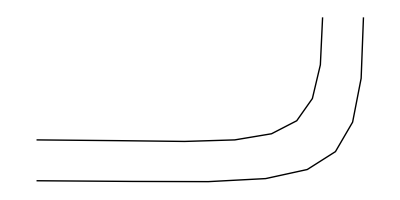

```mathematica
Module[{c1,c2},
(*OG BezierCurves*)
c1={{0,0},{1.75,0},{2,-0.15},{2,1}};
c2={{0,0.25},{1.5,0.25},{1.75,0.1},{1.75,1}};

Graphics[{Thick,BezierCurve@c1,BezierCurve@c2}]
]
```

## Make BezierCurve into a Line

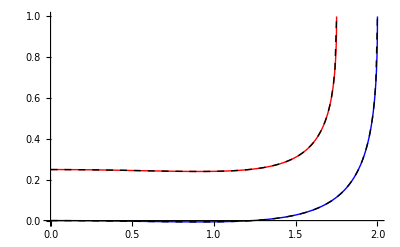

```mathematica
Module[{c1,c2,f,g},
c1={{0,0},{1.75,0},{2,-0.15},{2,1}};
c2={{0,0.25},{1.5,0.25},{1.75,0.1},{1.75,1}};

(*turn BezierCurve into a Line*)
f[c_]:=Quiet@Interpolation[BezierFunction[c][#]&/@Range[0,1,0.01]];
g[c_]:={#,f[c][#]}&/@Range[c[[1,1]],c[[-1,1]],0.01];

(*Graphics[{Thick,Line@g[c1],Line@g[c2]}];*)
Show[
Plot[f[c1][x],{x,c1[[1,1]],c1[[-1,1]]},PlotStyle->{Thick,Blue},PlotRange->All],
Plot[f[c2][x],{x,c2[[1,1]],c2[[-1,1]]},PlotStyle->{Thick,Red},PlotRange->All],
Graphics[{Thick,Dashed,Line@g[c1],Line@g[c2]}],
PlotRange->All]
]
```

## Get Lines ready for Polygon

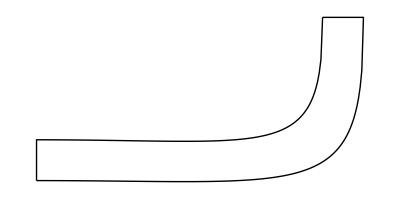

```mathematica
Module[{c1,c2,f,g,h1,h2},
c1={{0,0},{1.75,0},{2,-0.15},{2,1}};
c2={{0,0.25},{1.5,0.25},{1.75,0.1},{1.75,1}};

f[c_]:=Quiet@Interpolation[BezierFunction[c][#]&/@Range[0,1,0.01]];
g[c_]:={#,f[c][#]}&/@Range[c[[1,1]],c[[-1,1]],0.01];

(*ready for Polygon*)
h1=Join[g[c1],{c2[[-1]]}];h2=Join[{c1[[1]]},g@c2];

Graphics[{Thick,Line@h1,Line@h2}]
]
```

## Add Polygon and Points

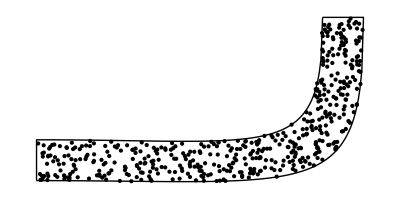

```mathematica
Module[{c1,c2,f,g,h1,h2},
c1={{0,0},{1.75,0},{2,-0.15},{2,1}};
c2={{0,0.25},{1.5,0.25},{1.75,0.1},{1.75,1}};

f[c_]:=Quiet@Interpolation[BezierFunction[c][#]&/@Range[0,1,0.01]];
g[c_]:={#,f[c][#]}&/@Range[c[[1,1]],c[[-1,1]],0.01];

h1=Join[g[c1],{c2[[-1]]}];h2=Join[{c1[[1]]},g@c2];

Graphics[{
Thick,Line@h1,Line@h2,
(*add points*)
Point@RandomPoint[Polygon[Join[h2,h1]],500]
}]
]
```